```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Solve[Simplify[Variance[StudentTDistribution[μ,Sqrt@σ,ν]],ν>2]==var,σ][[1,1,2]]
```

(var (-2+ν))/ν

```mathematica
customTDist[μ_,var_,ν_]:= Module[{σ=(var (-2+ν))/ν},StudentTDistribution[μ,Sqrt@σ,ν]]
```

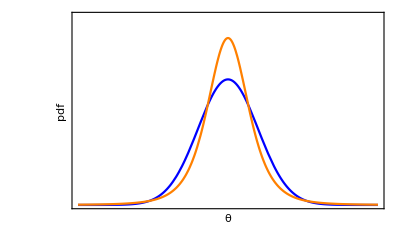

```mathematica
g1=Plot[{PDF[NormalDistribution[0,1],x],PDF[customTDist[0,1,4],x]},{x,-5,5},PlotRange->{Full,{0,0.6}},Frame->{True,True,False,False},AxesOrigin->{-5,0},FrameTicks->{None,None},FrameLabel->{"θ","pdf"},BaseStyle->Medium,PlotStyle->{Blue,Orange}]
```

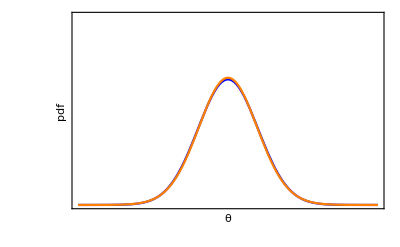

```mathematica
g2=Plot[{PDF[NormalDistribution[0,1],x],PDF[customTDist[0,1,60],x]},{x,-5,5},PlotRange->{Full,{0,0.6}},Frame->{True,True,False,False},AxesOrigin->{-5,0},FrameTicks->{None,None},FrameLabel->{"θ","pdf"},BaseStyle->Medium,PlotStyle->{Blue,Orange}]
```

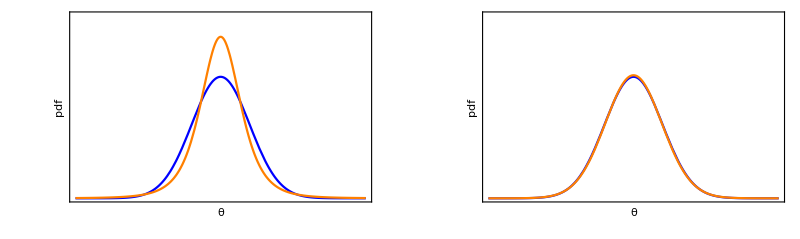

```mathematica
gFinal = Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_normalTPrior.pdf",gFinal]
```

Distributions_normalTPrior.pdf